```mathematica
data=Import["E:\\GoogleDriveData\\PHD_DATA\\2nd Year\\Spring_semester\\RA\\8th_week_25_02_01_032019\\equation fitting\\empirical_CDF.txt","Table"];
```

```mathematica
fit=NonlinearModelFit[data,R*Sinh[(t-t0)/τ0]+C,{R,t0,τ0,C},t]
```

FittedModel[0.363843+1.22083×10^-6 Sinh[1.09803 (-12.2482+t)]]

```mathematica
TableForm[fit["BestFitParameters"]]
```

R→1.22083×10^-6
t0→12.2482
τ0→0.910722
C→0.363843

```mathematica
First/@data
```

{0.111449444444444448,0.248840555555555565,0.346044722222222212,0.656522777777777788,0.664455000000000018,1.29130583333333338,1.33633722222222229,1.8231788888888889,6.19542833333333398,10.8026630555555556,21.3240797222222227,24.0110136111111139,24.0168611111111119,24.0172847222222252,24.0187788888888925,24.0206080555555559,24.0222261111111095,24.024485277777778,24.5713716666666642,24.5728872222222208,24.702461944444444,24.708210277777777,24.7097197222222214}

```mathematica
data//TableForm
```

0.111449444444444448 | 0.
0.248840555555555565 | 0.0434782608695652162
0.346044722222222212 | 0.0869565217391304324
0.656522777777777788 | 0.130434782608695649
0.664455000000000018 | 0.173913043478260865
1.29130583333333338 | 0.217391304347826081
1.33633722222222229 | 0.260869565217391297
1.8231788888888889 | 0.304347826086956541
6.19542833333333398 | 0.34782608695652173
10.8026630555555556 | 0.391304347826086918
21.3240797222222227 | 0.434782608695652162
24.0110136111111139 | 0.478260869565217406
24.0168611111111119 | 0.521739130434782594
24.0172847222222252 | 0.565217391304347783
24.0187788888888925 | 0.608695652173913082
24.0206080555555559 | 0.652173913043478271
24.0222261111111095 | 0.695652173913043459
24.024485277777778 | 0.739130434782608647
24.5713716666666642 | 0.782608695652173836
24.5728872222222208 | 0.826086956521739135
24.702461944444444 | 0.869565217391304324
24.708210277777777 | 0.913043478260869512
24.7097197222222214 | 0.956521739130434812

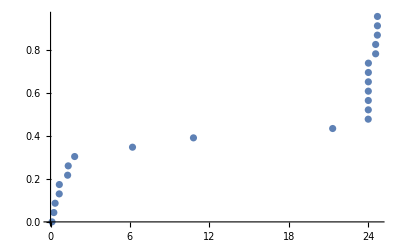

```mathematica
ListPlot[data]
```

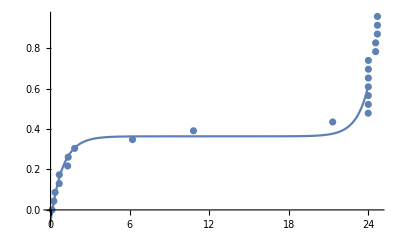

```mathematica
Show[Plot[fit[t],{t,0,24},PlotRange->All],ListPlot[data]]
```

```mathematica
f[t]= R*Sinh[(t-t0)/τ0]+C
```

C+R Sinh[(t-t0)/τ0]

```mathematica
D[f[t],t]
```

```mathematica
(R Cosh[(t-t0)/τ0])/τ0
```

```mathematica
fd[t]= R/τ0*Cosh[(t-t0)/τ0]
(*WolframAlpha["derivative of R*Sinh[(t - t0)/τ0]+C with respect to t"]*)
```

(R Cosh[(t-t0)/τ0])/τ0

```mathematica
Integrate[fd[t]*t,{t,0,24}]//N
```

R (-1. τ0 Cosh[(-24.+t0)/τ0]+τ0 Cosh[t0/τ0]-24. Sinh[(-24.+t0)/τ0])

Set::write: Tag Times in f t is Protected.

```mathematica
Integrate[fd[t]*t,t]//N
```

(R (-1. τ0^2 Cosh[(t-1. t0)/τ0]+t τ0 Sinh[(t-1. t0)/τ0]))/τ0

WolframAlphaQueryParseResults

(R Cosh[(t-t0)/τ0])/τ0

```mathematica
f2[t]= R*(1-B*exp[-a*t])
```

R (1-B exp[-a t])

```mathematica
D[f2[t],t]
```

a B R exp'[-a t]